# Introduction to cosmology

## FRW spacetime, Friedmann equations, ΛCDM model

```mathematica
(*import xTensor and xCoba*)
<<xAct`xTensor`;
<<xAct`xCoba`;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## FRW spacetime

For length scales L ~ 100 Mpc, the universe seems to be homogeneous and isotropic. The FRW spacetime captures this symmetry and is a fair model of expanding universe for L ~ 100 Mpc.

```mathematica
(*optional*)
$CovDFormat="Prefix";
$PrePrint=ScreenDollarIndices;
Options[MakeRule];
Options[ContractMetric];

(*define manifold and metric*)
dimension=4;                                
DefManifold[M,dimension,{b,c,d,i,j,k,l,u,v}];
DefMetric[-1,g[-b,-c],CD,{";","∇"},WeightedWithBasis->AIndex];
PrintAs[RiemannCD]^="R"; PrintAs[RicciCD]^="R"; PrintAs[RicciScalarCD]^="R"; PrintAs[ChristoffelCD]^="Γ"; PrintAs[EinsteinCD]^="G";

(*define an xCoba chart*)
DefChart[B,M,{0,1,2,3},{t[],x[],y[],z[]}];

(*scale factor a(t) and the spatially flat FRW metric*)
DefScalarFunction[a];
frw={{-1,0,0,0},{0,a[t[]]^2,0,0},{0,0,a[t[]]^2,0},{0,0,0,a[t[]]^2}};

(*tell xCoba that frw is the metric and to compute the curvature quantities*)
MetricInBasis[g,-B,frw];
MetricCompute[g,B,All,CVSimplify->Simplify];
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining symmetric metric tensor g[-b,-c].

** DefTensor: Defining antisymmetric tensor epsilong[-b,-c,-d,-i].

** DefTensor: Defining tetrametric Tetrag[-b,-c,-d,-i].

** DefTensor: Defining tetrametric Tetrag†[-b,-c,-d,-i].

** DefCovD: Defining covariant derivative CD[-b].

** DefTensor: Defining vanishing torsion tensor TorsionCD[b,-c,-d].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCD[-b,-c,-d,-i].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-b,-c].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-b,-c].

** DefTensor: Defining Weyl tensor WeylCD[-b,-c,-d,-i].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-b,-c].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefChart: Defining chart B.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping B.

** DefMapping: Defining inverse mapping iB.

** DefTensor: Defining mapping differential tensor diB[-a,iBb].

** DefTensor: Defining mapping differential tensor dB[-b,Ba].

** DefBasis: Defining basis B. Coordinated basis.

** DefCovD: Defining parallel derivative PDB[-b].

** DefTensor: Defining vanishing torsion tensor TorsionPDB[b,-c,-d].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDB[b,-c,-d].

** DefTensor: Defining vanishing Riemann tensor RiemannPDB[-b,-c,-d,i].

** DefTensor: Defining vanishing Ricci tensor RicciPDB[-b,-c].

** DefTensor: Defining antisymmetric +1 density etaUpB[b,c,d,i].

** DefTensor: Defining antisymmetric -1 density etaDownB[-b,-c,-d,-i].

** DefScalarFunction: Defining scalar function a.

Added independent rule g |   |  
0 | 0→-1 for tensor g

Added independent rule g |   |  
0 | 1→0 for tensor g

Added independent rule g |   |  
0 | 2→0 for tensor g

Added independent rule g |   |  
0 | 3→0 for tensor g

Added dependent rule g |   |  
1 | 0→g |   |  
0 | 1 for tensor g

Added independent rule g |   |  
1 | 1→a[t]^2 for tensor g

Added independent rule g |   |  
1 | 2→0 for tensor g

Added independent rule g |   |  
1 | 3→0 for tensor g

Added dependent rule g |   |  
2 | 0→g |   |  
0 | 2 for tensor g

Added dependent rule g |   |  
2 | 1→g |   |  
1 | 2 for tensor g

Added independent rule g |   |  
2 | 2→a[t]^2 for tensor g

Added independent rule g |   |  
2 | 3→0 for tensor g

Added dependent rule g |   |  
3 | 0→g |   |  
0 | 3 for tensor g

Added dependent rule g |   |  
3 | 1→g |   |  
1 | 3 for tensor g

Added dependent rule g |   |  
3 | 2→g |   |  
2 | 3 for tensor g

Added independent rule g |   |  
3 | 3→a[t]^2 for tensor g

** DefTensor: Defining weight +2 density DetgB[]. Determinant.

** DefTensor: Defining tensor ChristoffelCDPDB[b,-c,-d].

## FRW spacetime

Here is the spatially flat FRW metric.

```mathematica
"g_bc"==(g[-b,-c]//ToBasis[B]//ComponentArray//ToValues//MatrixForm)
```

g_bc==(-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | a[t]^2 | 0
0 | 0 | 0 | a[t]^2)

The line element for this is given by...

```mathematica
(*define infinitesimal spacetime displacement*)
DefTensor[dX[b],M];
dXcartesian={dt,dx,dy,dz};
ComponentValue[ComponentArray[dX[{b,B}]],dXcartesian];

(*line element*)
lineelementfrw=(g[-b,-c]dX[b]dX[c]//ToBasis[B]//TraceBasisDummy//ToValues);
"ds^2"==lineelementfrw
```

** DefTensor: Defining tensor dX[b].

Added independent rule dX | 0
 →dt for tensor dX

Added independent rule dX | 1
 →dx for tensor dX

Added independent rule dX | 2
 →dy for tensor dX

Added independent rule dX | 3
 →dz for tensor dX

ds^2==-dt^2+dx^2 a[t]^2+dy^2 a[t]^2+dz^2 a[t]^2

### Exercise time!

Exercise 1 “Homogeneity and isotropy”
	Prove that the FRW metric represents a spacetime that is invariant under spatial translation (x→x+x_0, y→y+y_0,z→z_0) and rotation (e.g., z→z,x→x cos ψ+y sinψ, y→-x sin ψ +y cosψ ). Is the FRW spacetime invariant under time translation/boost?
	
Exercise 2 “Maximally symmetric spaces in 3D”
	Maximally symmetric spaces/metrics are solutions to R_abcd=κ(g_ac g_bd-g_ad g_bc) where κ is a constant. Derive the most general maximally symmetric metric in three dimensions.

## Geodesics in FRW

To warmup, let us study the geodesics in the FRW spacetime. The geodesic equation is given by...

```mathematica
(*define the velocity vector V*)
DefTensor[V[b],M];
geodesics=CD[-c][V[-b]]V[b];

(*geodesic equation*)
geodesics==0
```

** DefTensor: Defining tensor V[b].

V | b
  ∇_c V |  
b==0

To proceed, we need to specify how the components of V^b depend on the coordinates. We do so as follows.

```mathematica
(*components of V^a*)
DefScalarFunction[Vt,PrintAs->"t_λ"];
DefScalarFunction[Vx,PrintAs->"x_λ"];
DefScalarFunction[Vy,PrintAs->"y_λ"];
DefScalarFunction[Vz,PrintAs->"z_λ"];
Vcomp={Vt[t[],x[],y[],z[]],Vx[t[],x[],y[],z[]],Vy[t[],x[],y[],z[]],Vz[t[],x[],y[],z[]]};
ComponentValue[ComponentArray[V[{b,B}]],Vcomp];
ChangeComponents[V[-{b,B}],V[{b,B}]];
```

** DefScalarFunction: Defining scalar function Vt.

** DefScalarFunction: Defining scalar function Vx.

** DefScalarFunction: Defining scalar function Vy.

** DefScalarFunction: Defining scalar function Vz.

Added independent rule V | 0
 →t_λ[t,x,y,z] for tensor V

Added independent rule V | 1
 →x_λ[t,x,y,z] for tensor V

Added independent rule V | 2
 →y_λ[t,x,y,z] for tensor V

Added independent rule V | 3
 →z_λ[t,x,y,z] for tensor V

Added independent rule V |  
0→g |   |  
0 | 0 V | 0
 +g |   |  
0 | 1 V | 1
 +g |   |  
0 | 2 V | 2
 +g |   |  
0 | 3 V | 3
  for tensor V

Added independent rule V |  
1→g |   |  
0 | 1 V | 0
 +g |   |  
1 | 1 V | 1
 +g |   |  
1 | 2 V | 2
 +g |   |  
1 | 3 V | 3
  for tensor V

Added independent rule V |  
2→g |   |  
0 | 2 V | 0
 +g |   |  
1 | 2 V | 1
 +g |   |  
2 | 2 V | 2
 +g |   |  
2 | 3 V | 3
  for tensor V

Added independent rule V |  
3→g |   |  
0 | 3 V | 0
 +g |   |  
1 | 3 V | 1
 +g |   |  
2 | 3 V | 2
 +g |   |  
3 | 3 V | 3
  for tensor V

Computed V |  
b→g |   |  
c | b V | c
  in 0.4761772 Seconds

For the FRW background, the components of the geodesic equation are...

```mathematica
geodcomp=geodesics//ToBasis[B]//ChristoffelToMetric//ToBasis[B]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplification;

(*independent components*)
geodcomptt=geodcomp[[1]];
geodcompxx=geodcomp[[2]];

"time component"==geodcomptt
"spatial components"==geodcompxx
```

time component==a[t] (x_λ[t,x,y,z]^2+y_λ[t,x,y,z]^2+z_λ[t,x,y,z]^2) a'[t]-t_λ[t,x,y,z] t_λ^(1,0,0,0)[t,x,y,z]+a[t]^2 (x_λ[t,x,y,z] x_λ^(1,0,0,0)[t,x,y,z]+y_λ[t,x,y,z] y_λ^(1,0,0,0)[t,x,y,z]+z_λ[t,x,y,z] z_λ^(1,0,0,0)[t,x,y,z])

spatial components==-t_λ[t,x,y,z] t_λ^(0,1,0,0)[t,x,y,z]+a[t]^2 (x_λ[t,x,y,z] x_λ^(0,1,0,0)[t,x,y,z]+y_λ[t,x,y,z] y_λ^(0,1,0,0)[t,x,y,z]+z_λ[t,x,y,z] z_λ^(0,1,0,0)[t,x,y,z])

Setting the comoving time t as the affine parameter and focusing on only the x direction (for simplicity)...

```mathematica
affinet={Vt[t[],x[],y[],z[]]->1,Derivative[1,0,0,0][Vt][t[],x[],y[],z[]]->0,Derivative[0,1,0,0][Vt][t[],x[],y[],z[]]->0};
xmotion={Vy[t[],x[],y[],z[]]->0,Vz[t[],x[],y[],z[]]->0,Derivative[0,1,0,0][Vy][t[],x[],y[],z[]]->0,Derivative[0,1,0,0][Vz][t[],x[],y[],z[]]->0};

Vt[t_,x_,y_,z_]:=Vt[t,x];
Vx[t_,x_,y_,z_]:=Vx[t,x];

(geodcomptt/.affinet/.xmotion//Simplify)==0
(geodcompxx/.affinet/.xmotion//Simplify)==0
```

a[t] x_λ[t,x] (x_λ[t,x] a'[t]+a[t] x_λ^(1,0)[t,x])==0

a[t]^2 x_λ[t,x] x_λ^(0,1)[t,x]==0

### Exercise time!

Exercise 3 “Hubble drag/flow”
	Show that the first equation implies p_x~1/a(t) where p_x=dx/dt. Also, use the second equation to show that p_x is a function only of the comoving time t, i.e., p_x is a constant.
	
Exercise 4 “Redshift”
	The redshift z of light that is emitted at time t_E and received at time t_0 is given by z=[λ(t_0)-λ(t_E)]/λ(t_E) where λ(t) is the wavelength of the photon at time t. Show that the redshift z is also given by z+1=a(t_0)/a(t_E). Hint: Consider photon geodesics; show that light that is emitted with wavelength λ_1 at time t_1 is observed at a later time t_0>t_1 with wavelength λ_0=λ_1 a(t_0)/a(t_1). 
	
Exercise 5 “Hubble law”
	For small redshifts/distances, derive Hubble’s law z=H_0 d+O(z^2) where H_0=a'(t_0)/a(t_0) is the Hubble parameter today. Hint: Expand a(t) about t_0 and use the result of exercise 2.

## FRW spacetime

For this section, we shall focus on the curvature quantities associated with the FRW metric.

The Ricci scalar is given by...

```mathematica
"R"==RicciScalarCD[]//ToBasis[B]//ToValues
```

R==(6 (a'[t]^2+a[t] a''[t]))/a[t]^2

The Kretschmann scalar (true curvature) is given by...

```mathematica
"K"==KretschmannCD[]//ToBasis[B]//ToValues
```

K==(12 (a'[t]^4+a[t]^2 a''[t]^2))/a[t]^4

The Einstein tensor is given by...

```mathematica
ET=EinsteinCD[-b,-c]//ToBasis[B]//ComponentArray//ToValues;
"G_bc"==(ET//MatrixForm)
```

G_bc==((3 a'[t]^2)/a[t]^2 | 0 | 0 | 0
0 | -a'[t]^2-2 a[t] a''[t] | 0 | 0
0 | 0 | -a'[t]^2-2 a[t] a''[t] | 0
0 | 0 | 0 | -a'[t]^2-2 a[t] a''[t])

By virtue of the homogeneity and isotropy inherent in the FRW metric, there are only two independent components in the Einstein tensor (and for all two-index tensors).

### Exercise time!

Exercise 6 “FRW Ricci tensor”
	Show explicitly that there are only two independent components in the Ricci tensor of the FRW metric.
	
Exercise 7 “Source-free expansion?”
	Solve the scale factor a(t) for the vacuum Einstein equation, G_bc=0. If the universe is expanding, then what does your solution suggest?

## Friedmann equations

Exercise 7 suggests that the spacetime cannot expand by itself, i.e., the observed expansion is assisted by the universe’s contents or matter components. The interaction between the expanding spacetime and the matter contents of the universe is captured by the Einstein equation in FRW metric or the Friedmann equations.

In this section, we shall derive the Friedmann equations and then solve it for the most physically motivated matter contents.

First off, we input the matter sources to the metric by first defining the tensor T and then assigning to this tensor the perfect fluid form in the chart B.

```mathematica
DefTensor[T[-b,-c],M,Symmetric[{-b,-c}]];
PF={{-ρ[t[]],0,0,0},{0,P[t[]],0,0},{0,0,P[t[]],0},{0,0,0,P[t[]]}};
ComponentValue[ComponentArray[T[{b,B},-{c,B}]],PF];

(*the perfect fluid*)
"(T^a)_b"==(T[b,-c]//ToBasis[B]//ComponentArray//ToValues//MatrixForm)
```

** DefTensor: Defining tensor T[-b,-c].

Added independent rule T | 0 |  
  | 0→-ρ[t] for tensor T

Added independent rule T | 0 |  
  | 1→0 for tensor T

Added independent rule T | 0 |  
  | 2→0 for tensor T

Added independent rule T | 0 |  
  | 3→0 for tensor T

Added dependent rule T | 1 |  
  | 0→T |   | 1
0 |   for tensor T

Added independent rule T |   | 1
0 |  →0 for tensor T

Added independent rule T | 1 |  
  | 1→P[t] for tensor T

Added independent rule T | 1 |  
  | 2→0 for tensor T

Added independent rule T | 1 |  
  | 3→0 for tensor T

Added dependent rule T | 2 |  
  | 0→T |   | 2
0 |   for tensor T

Added independent rule T |   | 2
0 |  →0 for tensor T

Added dependent rule T | 2 |  
  | 1→T |   | 2
1 |   for tensor T

Added independent rule T |   | 2
1 |  →0 for tensor T

Added independent rule T | 2 |  
  | 2→P[t] for tensor T

Added independent rule T | 2 |  
  | 3→0 for tensor T

Added dependent rule T | 3 |  
  | 0→T |   | 3
0 |   for tensor T

Added independent rule T |   | 3
0 |  →0 for tensor T

Added dependent rule T | 3 |  
  | 1→T |   | 3
1 |   for tensor T

Added independent rule T |   | 3
1 |  →0 for tensor T

Added dependent rule T | 3 |  
  | 2→T |   | 3
2 |   for tensor T

Added independent rule T |   | 3
2 |  →0 for tensor T

Added independent rule T | 3 |  
  | 3→P[t] for tensor T

(T^a)_b==(-ρ[t] | 0 | 0 | 0
0 | P[t] | 0 | 0
0 | 0 | P[t] | 0
0 | 0 | 0 | P[t])

The spatially-flat Friedman equations can be derived by equating the Einstein tensor to the perfect fluid stress-energy tensor.

```mathematica
(*compute up-down components of the Einstein tensor to match with the SET*)
ChangeComponents[EinsteinCD[{b,B},-{c,B}],EinsteinCD[-{b,B},-{c,B}]];
```

Added independent rule G | 0 |  
  | 0→G |   |  
0 | 0 g | 0 | 0
  |  +G |   |  
0 | 1 g | 0 | 1
  |  +G |   |  
0 | 2 g | 0 | 2
  |  +G |   |  
0 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added independent rule G | 0 |  
  | 1→G |   |  
0 | 1 g | 0 | 0
  |  +G |   |  
1 | 1 g | 0 | 1
  |  +G |   |  
1 | 2 g | 0 | 2
  |  +G |   |  
1 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added independent rule G | 0 |  
  | 2→G |   |  
0 | 2 g | 0 | 0
  |  +G |   |  
1 | 2 g | 0 | 1
  |  +G |   |  
2 | 2 g | 0 | 2
  |  +G |   |  
2 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added independent rule G | 0 |  
  | 3→G |   |  
0 | 3 g | 0 | 0
  |  +G |   |  
1 | 3 g | 0 | 1
  |  +G |   |  
2 | 3 g | 0 | 2
  |  +G |   |  
3 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 1 |  
  | 0→G |   | 1
0 |   for tensor EinsteinCD

Added independent rule G |   | 1
0 |  →G |   |  
0 | 0 g | 0 | 1
  |  +G |   |  
0 | 1 g | 1 | 1
  |  +G |   |  
0 | 2 g | 1 | 2
  |  +G |   |  
0 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added independent rule G | 1 |  
  | 1→G |   |  
0 | 1 g | 0 | 1
  |  +G |   |  
1 | 1 g | 1 | 1
  |  +G |   |  
1 | 2 g | 1 | 2
  |  +G |   |  
1 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added independent rule G | 1 |  
  | 2→G |   |  
0 | 2 g | 0 | 1
  |  +G |   |  
1 | 2 g | 1 | 1
  |  +G |   |  
2 | 2 g | 1 | 2
  |  +G |   |  
2 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added independent rule G | 1 |  
  | 3→G |   |  
0 | 3 g | 0 | 1
  |  +G |   |  
1 | 3 g | 1 | 1
  |  +G |   |  
2 | 3 g | 1 | 2
  |  +G |   |  
3 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 2 |  
  | 0→G |   | 2
0 |   for tensor EinsteinCD

Added independent rule G |   | 2
0 |  →G |   |  
0 | 0 g | 0 | 2
  |  +G |   |  
0 | 1 g | 1 | 2
  |  +G |   |  
0 | 2 g | 2 | 2
  |  +G |   |  
0 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 2 |  
  | 1→G |   | 2
1 |   for tensor EinsteinCD

Added independent rule G |   | 2
1 |  →G |   |  
0 | 1 g | 0 | 2
  |  +G |   |  
1 | 1 g | 1 | 2
  |  +G |   |  
1 | 2 g | 2 | 2
  |  +G |   |  
1 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added independent rule G | 2 |  
  | 2→G |   |  
0 | 2 g | 0 | 2
  |  +G |   |  
1 | 2 g | 1 | 2
  |  +G |   |  
2 | 2 g | 2 | 2
  |  +G |   |  
2 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added independent rule G | 2 |  
  | 3→G |   |  
0 | 3 g | 0 | 2
  |  +G |   |  
1 | 3 g | 1 | 2
  |  +G |   |  
2 | 3 g | 2 | 2
  |  +G |   |  
3 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 3 |  
  | 0→G |   | 3
0 |   for tensor EinsteinCD

Added independent rule G |   | 3
0 |  →G |   |  
0 | 0 g | 0 | 3
  |  +G |   |  
0 | 1 g | 1 | 3
  |  +G |   |  
0 | 2 g | 2 | 3
  |  +G |   |  
0 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 3 |  
  | 1→G |   | 3
1 |   for tensor EinsteinCD

Added independent rule G |   | 3
1 |  →G |   |  
0 | 1 g | 0 | 3
  |  +G |   |  
1 | 1 g | 1 | 3
  |  +G |   |  
1 | 2 g | 2 | 3
  |  +G |   |  
1 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 3 |  
  | 2→G |   | 3
2 |   for tensor EinsteinCD

Added independent rule G |   | 3
2 |  →G |   |  
0 | 2 g | 0 | 3
  |  +G |   |  
1 | 2 g | 1 | 3
  |  +G |   |  
2 | 2 g | 2 | 3
  |  +G |   |  
2 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added independent rule G | 3 |  
  | 3→G |   |  
0 | 3 g | 0 | 3
  |  +G |   |  
1 | 3 g | 1 | 3
  |  +G |   |  
2 | 3 g | 2 | 3
  |  +G |   |  
3 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added dependent rule G |   | 0
0 |  →G | 0 |  
  | 0 for tensor EinsteinCD

Added dependent rule G |   | 0
1 |  →G | 0 |  
  | 1 for tensor EinsteinCD

Added dependent rule G |   | 1
1 |  →G | 1 |  
  | 1 for tensor EinsteinCD

Added dependent rule G |   | 0
2 |  →G | 0 |  
  | 2 for tensor EinsteinCD

Added dependent rule G |   | 1
2 |  →G | 1 |  
  | 2 for tensor EinsteinCD

Added dependent rule G |   | 2
2 |  →G | 2 |  
  | 2 for tensor EinsteinCD

Added dependent rule G |   | 0
3 |  →G | 0 |  
  | 3 for tensor EinsteinCD

Added dependent rule G |   | 1
3 |  →G | 1 |  
  | 3 for tensor EinsteinCD

Added dependent rule G |   | 2
3 |  →G | 2 |  
  | 3 for tensor EinsteinCD

Added dependent rule G |   | 3
3 |  →G | 3 |  
  | 3 for tensor EinsteinCD

Computed G | b |  
  | c→G |   |  
d | c g | b | d
  |   in 3.6130182 Seconds

Finally, we obtain the Friedman equations from the following.

```mathematica
LHS=(EinsteinCD[b,-c]//ToBasis[B]//ComponentArray//ToValues//ToValues);
RHS=(8π T[b,-c]//ToBasis[B]//ComponentArray//ToValues);

(*Friedman equations*)
(LHS//MatrixForm)==(RHS//MatrixForm)
```

(-(3 a'[t]^2)/a[t]^2 | 0 | 0 | 0
0 | (-a'[t]^2-2 a[t] a''[t])/a[t]^2 | 0 | 0
0 | 0 | (-a'[t]^2-2 a[t] a''[t])/a[t]^2 | 0
0 | 0 | 0 | (-a'[t]^2-2 a[t] a''[t])/a[t]^2)==(-8 π ρ[t] | 0 | 0 | 0
0 | 8 π P[t] | 0 | 0
0 | 0 | 8 π P[t] | 0
0 | 0 | 0 | 8 π P[t])

The independent equations from the above are...

```mathematica
removebrackets=t[]->t;

(*first Friedman equation*)
friedman1=(LHS[[1,1]]/.removebrackets)==(RHS[[1,1]]/.removebrackets)

(*second Friedman equation*)
friedman2=(LHS[[2,2]]/.removebrackets)==(RHS[[2,2]]/.removebrackets)
```

-(3 a'[t]^2)/a[t]^2==-8 π ρ[t]

(-a'[t]^2-2 a[t] a''[t])/a[t]^2==8 π P[t]

Typically, we express the Friedmann equations in terms of the Hubble parameter H=a'/a. We can obtain the Friedman equations in terms of the Hubble parameter by imposing the following rules.

```mathematica
AtoHubble=Solve[{H[t]==a'[t]/a[t],H'[t]==D[a'[t]/a[t],t]},{a'[t],a''[t]}][[1]];
```

In terms of the Hubble parameter, the Friedmann equations are given by the following.

```mathematica
friedman1/.AtoHubble//Simplify
friedman2/.AtoHubble//Simplify
```

3 H[t]^2==8 π ρ[t]

3 H[t]^2+8 π P[t]+2 H'[t]==0

### Exercise time!

Exercise 8 “Conservation of energy I”
	Show that ρ'+3(ρ + P)H=0 follows from the Friedmann equations.
	
Exercise 9 “Conservation of energy II”
	Derive the ρ'+3(ρ + P)H=0 by using the first law of thermodynamics, dU=dQ-PdV. Hint: Assume (and then justify later) that the expansion of the universe is an adiabatic thermal process, dQ=0.
	
Exercise 10 “Conservation of energy III”
	Derive the ρ'+3(ρ + P)H=0 from the conservation of stress-energy tensor, ∇_b T_a^b=0.

## Friedmann equations

In this slide, we present the most elementary solutions of the Friedmann equations. We restrict our attention to cases with P/ρ=w where w is a constant that we refer to as the equation of state.

We start by solving the conservation of energy expression for the Hubble parameter.

```mathematica
P[t_]:=w ρ[t]
coe=ρ'[t]+3(ρ[t]+P[t])H[t]==0;

(*the Hubble constant*)
"H(t)"==H[t]/.Solve[coe,H[t]][[1]]
```

H(t)==-ρ'[t]/(3 (1+w) ρ[t])

This expression leads to the energy density...

```mathematica
arule=DSolve[a'[t]/a[t]==(H[t]/.Solve[coe,H[t]][[1]]),ρ,t][[1]];
"ρ(t)"==ρ[t]/.arule
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

ρ(t)==a[t]^(-3 (1+w)) C[1]

Alternatively, it is nice to write this down as...

```mathematica
"(d(log ρ))/(d(log a))"==(Log[(ρ[t]/.arule/.C[1]->ρ̄)/ρ̄]/.Log[a_ b_]->Log[a]+Log[b]/.Log[a_^b_]->b Log[a])/Log[a[t]]
```

(d(log ρ))/(d(log a))==-3 (1+w)

### Energy density in different eras of the universe’s history

Radiation-dominated universe:

```mathematica
"ρ(t)"==ρ[t]/.arule/.w->1/3
```

ρ(t)==C[1]/a[t]^4

Matter-dominated universe:

```mathematica
"ρ(t)"==ρ[t]/.arule/.w->0
```

ρ(t)==C[1]/a[t]^3

Vacuum-dominated universe:

```mathematica
"ρ(t)"==ρ[t]/.arule/.w->-1
```

ρ(t)==C[1]

### Exercise time!

Exercise 11 “Coincidence problem”
	Make a plot of d(log ρ)/d(log a) for w=1/3,0, and -1 and identify the different eras (e.g., radiation-domination, matter-domination) in the universe’s history. Use the y-intercepts y_int=3 for w=1/3, 0 and y_int=1 for w=-1.

```mathematica
(*line[x_,w_,yint_]:=-3(1+w)x+yint
Plot[{line[x,1/3,3],line[x,0,3],line[x,-1,1]},{x,-1,1},PlotRange->All,AxesStyle->Directive[Red,30],LabelStyle->Directive[Red,30],Frame->{{True,False},{False,True}},FrameLabel->{{"log(ρ)",None},{None,"log(a)"}},FrameTicks->{{-1,0,1},{-1,0,2,4,6}},Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"w = 1/3","w = 0","w = -1"},PlotStyle->{Thickness[0.012],{Dashing[Large],Thickness[0.015]},{Dashing[Small],Thickness[0.02]}},ImageSize->Large]*)
```

## Accelerating universe scenario

In this section, we derive conditions on the equation of state w for an accelerating universe picture. Once more, the Friedmann equations are...

```mathematica
friedman1
friedman2
```

-(3 a'[t]^2)/a[t]^2==-8 π ρ[t]

(-a'[t]^2-2 a[t] a''[t])/a[t]^2==8 π w ρ[t]

An expanding universe means that da/dt>0 and an accelerating universe means that d^2 a/dt^2>0. To see what this implies according to the Friedmann equations, we solve for a''(t).

```mathematica
solfriedman1=Solve[friedman1,a'[t]][[1]];
solfriedman2=Solve[friedman2,a''[t]][[1]];
"a''[t]"==a''[t]/.solfriedman2/.solfriedman1//Simplify
```

a''[t]==-4/3 π (1+3 w) a[t] ρ[t]

This solution shows that w<-1/3 for the universe to exhibit acceleration. No such ordinary matter, however, satisfies this equation of state. The source and fundamental meaning to the observed late-time acceleration of the universe today is what we refer to as “dark energy”.

Suppose that H>0 and H' >0. Let us find out the conditions that lead to such Hubble parameter and proceed by eliminating the energy density in the expressions. In this way, we find that...

```mathematica
friedmann1H=friedman1/.AtoHubble//Simplify;
friedmann2H=friedman2/.AtoHubble//Simplify;

solfe1=Solve[friedmann1H,ρ[t]][[1]];
(*one equation for Friedmann equations*)
friedmann2H/.solfe1//Simplify
```

3 (1+w) H[t]^2+2 H'[t]==0

From this we can obtain...

```mathematica
"H'[t]"==(H'[t]/.Solve[friedmann2H/.solfe1,H'[t]][[1]]//Simplify)
```

H'[t]==-3/2 (1+w) H[t]^2

For H'>0 we see that w<-1. For these equations of state, we are crossing the phantom divide.

### Exercise time!

Exercise 12 “Nondimensionalizing the first Friedmann equation”
	Rewrite the first Friedmann equations as a'(t)=a(t)H_0 √(Ω_rad a^-4+Ω_(dm/bar) a^-3+Ω_Λ) where Ω_i=ρ_i/3 H_0^2 is the density parameter for specie i (e.g., baryon and dark matter) and H_0 is the present value of the Hubble parameter.

## ΛCDM expansion history

In the ΛCDM model, the universe’s energy density is mainly dark energy (~70%), dark matter (~25%), and ordinary matter (baryon, neutrinos, radiation ~5%). We can solve for the scale factor of the  ΛCDM model by using the first Friedmann equations.

```mathematica
Clear[P,ρ];
$Assumptions=H>0;
ρ[t_]:=(3 H^2)/(8π)Ω[a[t]]
friedman1recast=a'[t]==(a'[t]/.Solve[friedman1,a'[t]][[2]]//Simplify);

(*ΛCDM parameters obtained from Planck mission[Table 2 of arXiv:1807.06209]*)
Ω[x_]:=Ωr/x^4+Ωm/x^3+ΩΛ;ΩΛ=689/1000;Ωm=311/1000;Ωr=0;H=1;

(*the recast first Friedmann equation*)
friedman1recast
```

a'[t]==√(689/1000+311/(1000 a[t]^3)) a[t]

The expansion history is obtained as follows.

```mathematica
(*numerically solving for the scale factor*)
alcdm=NDSolve[{friedman1recast,a[1]==1},a,{t,0,2}];
Plot[{a[t]/.alcdm},{t,0,1},ColorFunction->(ColorData["Rainbow"][Rescale[#2,{0,1}]]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{"t","a(t)"},AxesStyle->Directive[Red,30],LabelStyle->Directive[Black,Bold],Ticks->Automatic,TicksStyle->Directive[Pink,30],PlotStyle->{Thickness[0.01]},ImageSize->Large]
```

NDSolve::ndsz: At t == 0.0455878, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

As for the energy density, we can simply use our expression earlier and then apply the solution of the first Friedmann equation.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

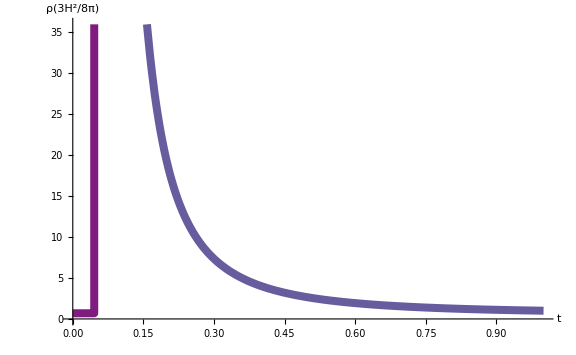

```mathematica
Plot[{ρ[t]/((3 H^2)/(8π))/.alcdm},{t,0,1},ColorFunction->(ColorData["Rainbow"][Rescale[#2,{0,1}]]&),AxesLabel->{"t","ρ(3H^2/8π)"},AxesStyle->Directive[Red,30],LabelStyle->Directive[Black,Bold],Ticks->Automatic,TicksStyle->Directive[Pink,30],PlotStyle->{Thickness[0.01]},ImageSize->Large]
```

### Exercise time!

Exercise 13 “Does the universe feel pressure?”
	Plot the pressure of the fluid as a function of the time t in the ΛCDM model.

## Distances in cosmology

In cosmology, several measures of distance are used in practice: (i) comoving distance, (ii) physical distance, (iii) luminosity distance, and (iv) angular diameter distance.

Recall the line element in FRW metric (Cartesian coordinates).

```mathematica
"ds^2"==lineelementfrw
```

ds^2==-dt^2+dx^2 a[t]^2+dy^2 a[t]^2+dz^2 a[t]^2

The comoving/coordinate distance is given simply by dσ^2=dx^2+dy^2+dz^2. On the other hand, the physical distance is dσ_p^2=(a(t))^2 dσ^2.

### Example “Hubble law”

Consider two points/galaxies on the x-axis that are separated by a constant comoving distance of X. This means that dx=0. Is the velocity between the two points zero?

```mathematica
Clear[H]
vel=D[a[t]X,t]/.a'[t]->H[t]a[t]/.X->Subscript[X, p]/a[t];
"V_p"==vel
```

V_p==H[t] X_p

Thus, comoving galaxies are moving away from each other with a rate given by the Hubble parameter.

### Luminosity distance

Before the CMB, the information about the universe was obtained from distance measurements. The luminosity distance played a central role in observing the accelerated expansion. 

To derive the (dynamical) expression for the luminosity distance, we start with the nondimensionalized first Friedmann equation.

```mathematica
Clear[Ωm,ΩΛ,Ωr];
friedman1recast
```

a'[t]==H √(ΩΛ+Ωr/a[t]^4+Ωm/a[t]^3) a[t]

From this, we can obtain an expression for the comoving time as a function of the scale factor x.

```mathematica
trule=Solve[(friedman1recast/.a'[t]->dx/dt/.a[t]->x),dt][[1]];
"dt"==(dt/.trule//Simplify)
```

dt==dx/(H x √(Ωm/x^3+Ωr/x^4+ΩΛ))

In the FRW metric, light travels a coordinate distance dr=dt/a(t) for a given time dt. So, the coordinate distance r travelled by light can be expressed in terms of the scale factor as...

```mathematica
"dr"==(dt/x/.trule//Simplify)
```

dr==dx/(H x^2 √(Ωm/x^3+Ωr/x^4+ΩΛ))

It is conventional to express this in terms of the redshift. This can be achieved by using z+1=1/x. The distance r(z) travelled by light at redshift z is given by...

```mathematica
R[z_]:=NIntegrate[1/(H x^2 √(Ωm/x^3+Ωr/x^4+ΩΛ)),{x,1/(1+z),1}]
```

Finally, the luminosity distance D_L is equal to (1+z)R(z).

```mathematica
DL[z_]:=(1+z)R[z]
```

Here is a plot of the luminosity distance as a function of redshift from z=0 to z=1 for the ΛCDM parameters.

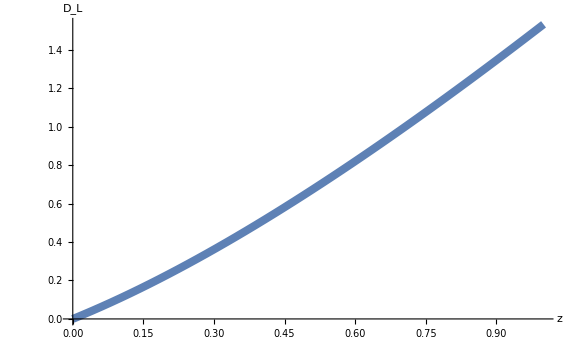

```mathematica
Clear[H,ΩΛ,Ωm,Ωr]
ΩΛ=689/1000;Ωm=311/1000;Ωr=0;H=1;
Plot[DL[z],{z,0,1},AxesLabel->{"z","D_L"},AxesStyle->Directive[Red,30],LabelStyle->Directive[Black,Bold],Ticks->Automatic,TicksStyle->Directive[Pink,30],PlotStyle->{Thickness[0.01]},ImageSize->Large]
```

### Exercise time!

Exercise 14 “The age of the universe”
	Estimate the age of the universe by using the ΛCDM parameters [Table 2 of arXiv:1807.06209] ΩΛ=689/1000,Ωm=311/1000,Ωr=0 and the approximate Hubble constant H_0=70 km/s/Mpc.

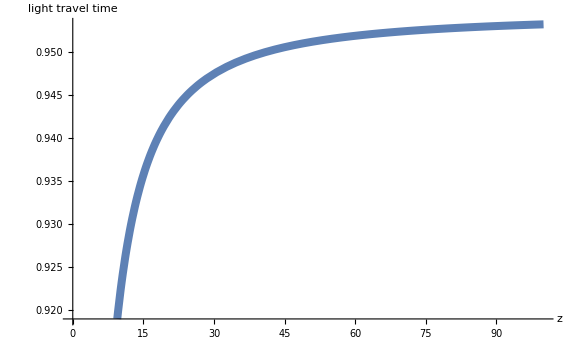

```mathematica
Clear[H,ΩΛ,Ωm,Ωr]
ΩΛ=689/1000;Ωm=311/1000;Ωr=0;H=1;
(*light travel time from redshift z to redshift 0*)
LTT[z_]:=NIntegrate[1/(H x √(Ωm/x^3+Ωr/x^4+ΩΛ)),{x,1/(1+z),1}]
(*age of the universe is LTT(∞)*)
Plot[LTT[z],{z,0,100},AxesLabel->{"z","light travel time"},AxesStyle->Directive[Red,30],LabelStyle->Directive[Red,Bold],Ticks->Automatic,TicksStyle->Directive[Pink,30],PlotStyle->{Thickness[0.01]},ImageSize->Large]
```

## Distances in cosmology

In practice, the distance-modulus is typically used as a distance indicator instead of the luminosity distance. The distance-modulus and the luminosity distance are related as follows.

```mathematica
(*DM is the distance modulus and D (in pc) is the luminosity distance*)
DM[z_]:=5 (-1+Log[DL[z]]/Log[10])
```

Using the expression for the luminosity distance in terms of the redshift, we can then also express the distance-modulus in terms of the redshift. But before doing so, let us express the Hubble parameter in conventional units.

```mathematica
Clear[H]
H=70(*km/(Mpc s)*)(1(*Mpc*))/(10^6(*pc*))(1(*pc*))/(3.086*10^13(*km*));
(*the age of the universe is roughly the reciprocal of the Hubble parameter*)
1/H(*s*)(1(*hr*))/(3600(*s*))(1(*day*))/(24(*hr*))(1(*yr*))/(365(*day*))(1(*Gyr*))/(10^9(*yr*))" billion years"
```

13.9795  billion years

In this time scale, light travels a distance of c/H_0 which is...

```mathematica
Hubbleradius=(3*10^8)/H(*m*)(1(*km*))/(1000(*m*))(1(*pc*))/(3.086*10^13(*km*));
Hubbleradius " parsecs"
```

4.28571×10^9  parsecs

For the ΛCDM parameters, here is a plot of the distance-modulus in terms of the redshift.

NIntegrate::nlim: x = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

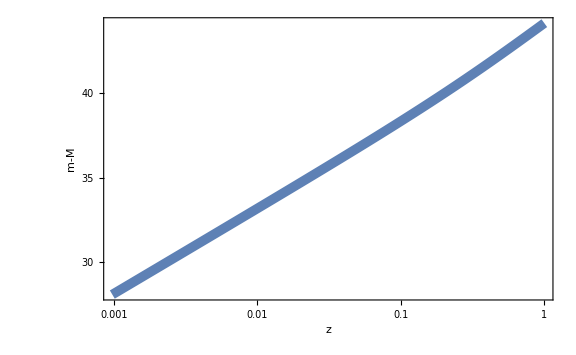

```mathematica
H=1;
LogLinearPlot[5 (-1+Log[Hubbleradius DL[z]]/Log[10]),{z,0,1},PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Pink,30],Frame->{{True,False},{True,False}},FrameLabel->{{"m-M",None},{"z",None}},FrameTicks->{{0.01,0.1,0.5,1},{30,35,40,45}},Ticks->Automatic,TicksStyle->Directive[Pink,30],PlotStyle->{Thickness[0.012]},ImageSize->Large]
```

### Homework!

Download the data of the Supernova Cosmology Project and the High-z Supernova Search Team for the distance-modulus as a function of redshift and visually obtain the parameters of the ΛCDM by using Manipulate[].